# Generic Natario warp drive and deflector shield with no time dependence

## Geometric quantities

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

## Vincent Geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

```mathematica
ClearAll[vincentPU]
vincentPU=energy(nU+Join[{0},VU]);

ClearAll[vincentNorm]
vincentNorm=FullSimplify[Solve[Sum[gLL[[a,b]]vincentPU[[a]]vincentPU[[b]],{a,1,4},{b,1,4}]==(-δ),energy]]
```

{{energy→-(√δ)/(√(1-velx^2-vely^2-velz^2))},{energy→(√δ)/(√(1-velx^2-vely^2-velz^2))}}

## Transition function

```mathematica
ClearAll[deg,poly];
deg=1;
poly[x_]=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==0
(*Derivative[1][poly][x0]==0,
Derivative[1][poly][x0+dx]==0,
Derivative[2][poly][x0]==0,
Derivative[2][poly][x0+dx]==0,
Derivative[3][poly][x0]==0,
Derivative[3][poly][x0+dx]==0*)
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs];

ClearAll[polyTrans];
polyTrans[x_,y0_,x0_,dx_]=Piecewise[
{
{y0,x<x0},
{0,x>(x0+dx)},
{polyWithCs,True}
}
]
```

Piecewise[{{y0, x<x0}, {0, x>dx+x0}, {((dx-x+x0) y0)/dx, True}}]

```mathematica
D[polyTrans[x,y0,x0,dx],x]//FullSimplify
```

Piecewise[{{0, x<x0||dx+x0<x}, {-y0/dx, True}}]

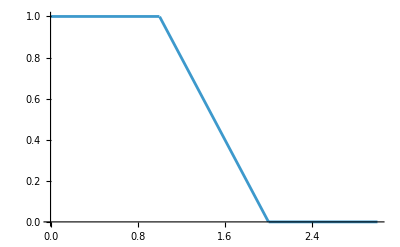

```mathematica
Plot[polyTrans[x,1,1,1],{x,0,3}]
```

## Fixed points

```mathematica
ClearAll[α];
α[t_,x_,y_,z_]:=1;

ClearAll[r];
r[t_,x_,y_,z_]:=Sqrt[((x-u*t)^2+y^2+z^2)];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]:=u0*f[r[t,x,y,z],1,radius,sigma];

vy[t_,x_,y_,z_]:=0;
vz[t_,x_,y_,z_]:=0;

ClearAll[f];
(*f[x_,y0_,x0_,dx_]=polyTrans[x,y0,x0,dx];*)
f[x_,y0_,x0_,dx_]=((dx-x+x0) y0)/dx;

ClearAll[rule];
rule={vely->0,velz->0,y->0,z->0};

Print["dXdt = ",FullSimplify[dXudt[[1]]//.rule,{t∈Reals,x∈Reals,t>=0}]]
Print["dYdt = ",FullSimplify[dXudt[[2]]//.rule,{t∈Reals,x∈Reals,t>=0}]]
Print["dZdt = ",FullSimplify[dXudt[[3]]//.rule,{t∈Reals,x∈Reals,t>=0}]]

Print["dVXdt = ",FullSimplify[dVUdt[[1]]//.rule,{t∈Reals,x∈Reals,t>=0}]]
Print["dVYdt = ",FullSimplify[dVUdt[[2]]//.rule,{t∈Reals,x∈Reals,t>=0}]]
Print["dVZdt = ",FullSimplify[dVUdt[[3]]//.rule,{t∈Reals,x∈Reals,t>=0}]]
(*Print["E = ",dEdt//.rule]*)

ClearAll[rule];
ClearAll[f];
ClearAll[vx,vy,vz];
ClearAll[r,ρy,ρz];
ClearAll[α];
```

dXdt = velx+(u0 (radius+sigma-√((-t u+x)^2)))/sigma

dYdt = 0

dZdt = 0

dVXdt = (u0 velx (-1+velx^2) (t u-x))/(sigma √((-t u+x)^2))

dVYdt = 0

dVZdt = 0

```mathematica
DSolve[
{
X'[t]==velx+(u0 (radius+sigma-√((-t u+x)^2)))/sigma ,
VX'[t]==(u0 velx (-1+velx^2) (t u-x))/(sigma √((-t u+x)^2)),
X[0]==x0,
VX[0]==VX0
}//.{velx->VX[t],x->X[t]},
{X[t],VX[t]},
t
]
```

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.